## Formal Rule Proof/Analysis

Derived variables

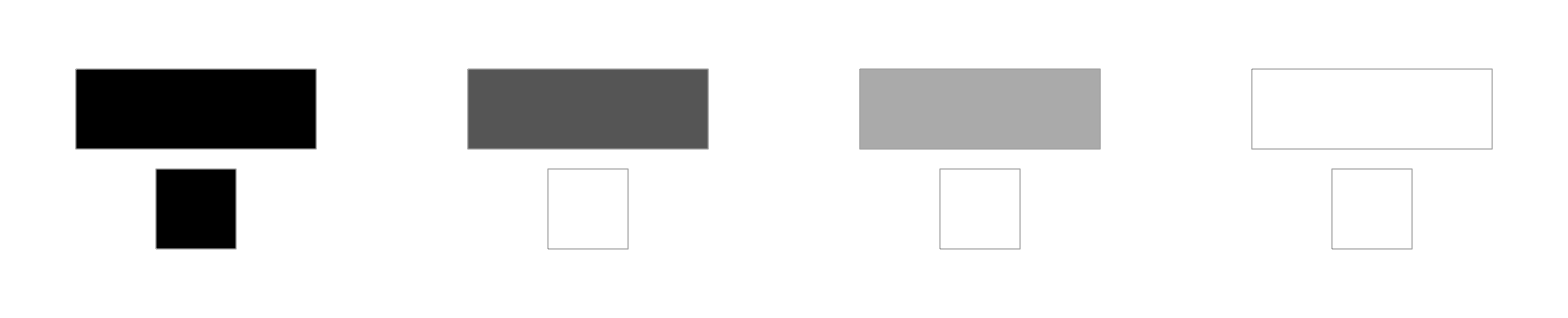

```mathematica
RulePlot[CellularAutomaton[{8, {2, 1}, 1}]]
```

Let the number of alive cells in a given time step t be denoted N(t).
lemma: N(t) is strictly decreasing or zero
proof:
x(t + 1, i) = (x(t, i-1) + x(t, i) + x(t, i+1) == 3)
Therefore, x(t + 1, i) implies x(t, i). Therefore, once a position turns off, it can never turn back on.
If N(t) is zero, then no cells are off, so none can turn on, so N(t+1) is zero.
Otherwise, there exists a neighborhood with sum of three. Therefore there exists a contiguous range of all 1s. Consider the end of this range. Applying the rule, we get that the rightmost end turns off. Therefore, N(t + 1) <= N(t) - 1. Proof complete.

```mathematica
Table[Labeled[ArrayPlot[CellularAutomaton[{i, {2, 1}, 2}, {RandomInteger[1, 100], 0}, 100]], i], {i, 0, 63}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

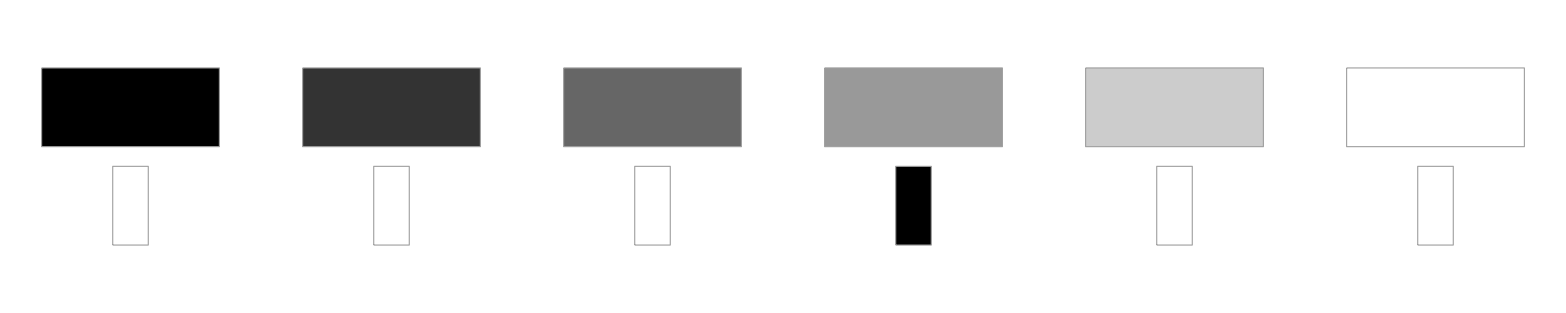

```mathematica
RulePlot[CellularAutomaton[{4, {2, 1}, 2}]]
```